# NLIT (Not-LIT) 9/9/21

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5,1.5};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-5);
dH=1;
```

```mathematica
ImgSize=900;
hbarc=197.32858;
mn=938.3;
hbarsqO2m=hbarc^2/(2 mn);
αfine=1./137.;
hat[l_]:=Sqrt[2 l+1];

resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/latestresults_FSon";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/kette_repo/ComptonLIT/systems/latestresults_FSon
in
float64=Real64
format for
N_bases=9
evolved bases for the expansion of the final state.

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
evm=(Transpose[invtrafma].norm).invtrafma;
evm=(evm+Transpose[evm])/2;(* symmetrize for stability *)
evv=Eigenvalues[evm];
Print["MinMax[Re] = ",MinMax[Re[evv]]];
Print["MinMax[Im] = ",MinMax[Im[evv]]];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=He3NormHamMat[[Range[1,Length[He3NormHamMat],2]]];
ActiveBasVHe3=ReadList["./Ssigbasv3heLIT_npp0.5^+.dat"];

BareDims=Table[ReadList["./BareBasDims_"<>ToString[nn]<>".dat"],{nn,Range[0,anzBas-1]}]
(*He3NormHamMat=tmp;*)
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
Print["N_(helion - full) = ",He3BasisDim];
Print["N_(helion - active) = ",Length[ActiveBasVHe3]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
MinMax[Eigenvalues[He3Norm]]
```

{{60,95},{60,96},{60,86},{60,94},{60,84},{60,98},{60,96},{60,102},{60,102}}

N_(helion - full) = 57

N_(helion - active) = 57

{2.38966×10^-8,17.2836}

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
```

min/max: {2.38966×10^-8,17.2836}

(min/max) discarded elements: 1 {2.38966×10^-8,2.38966×10^-8}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

B(^3He) = -8.54733

Dim_full^helion = 57=^!57   ;     Dim_(non - singular)^helion = 56

Norm=1.

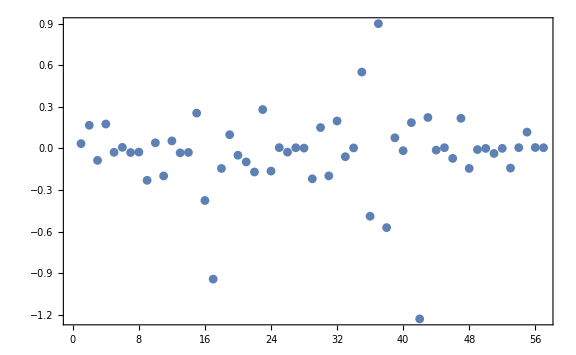
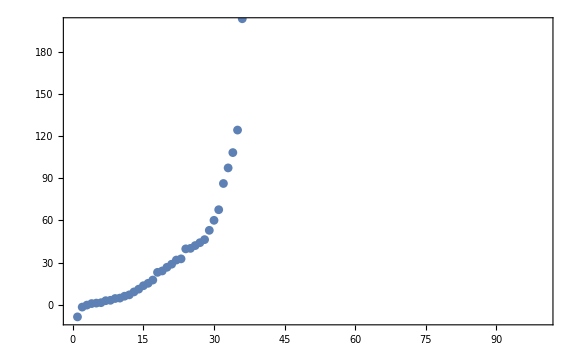
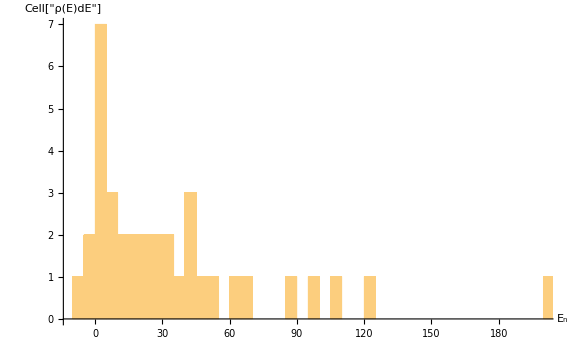
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYHe3[[1]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0t][[1]]]

fullv0=He3Nmhi.v0t;
Print["Norm=",fullv0.He3Norm.fullv0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM basis vector}~n",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

LitNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

ActiveBasVFin=Table[Table[ReadList["Ssigbasv3heLIT_"<>ToString[Subscript[I, n][[Inn]]]<>"^-_BasNR-"<>ToString[nn]<>".dat"],{nn,Range[0,anzBas-1]}],{Inn,Range[Length[Subscript[I, n]]]}];

LITbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["N_(final - full) = ",LITbasisDim];
LitNorm=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[1;;LITbasisDim[[Inn]][[#]]^2]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
LitHam=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[LITbasisDim[[Inn]][[#]]^2+1;;]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];

Print["N_(final - active) = ",Length[#]&/@ActiveBasVFin];
Print["min/max Norm EV = ",Table[MinMax[Eigenvalues[LitNorm[[Inn]][[#]]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}]];
```

N_(final - full) = {{73,72,78,75,68,84,84,72,78},{92,94,85,94,83,98,96,102,102}}

N_(final - active) = {9,9}

min/max Norm EV = {{{4.21749×10^-6,16.2682},{0.000157061,15.6256},{1.83482×10^-6,20.5083},{4.50876×10^-6,14.1418},{8.01172×10^-7,14.2999},{9.33313×10^-8,19.0046},{0.0000123287,19.4089},{1.71138×10^-6,20.9142},{5.72172×10^-7,19.3788}},{{1.146×10^-6,15.6414},{0.0000224594,17.8854},{0.000134739,17.4464},{2.06317×10^-6,15.8571},{0.0000914409,16.7881},{1.42079×10^-6,19.025},{8.13434×10^-8,17.8369},{6.07216×10^-6,21.7016},{0.0000157179,18.8884}}}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

```mathematica
dE=2.;
plts={};
Do[
Do[
Print["=== I_n=",Subscript[I, n][[nj]],"  BasNR: ",nb," ==="];
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[nb]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]][[nb]],thresholdLIT];
orderedEVSYLIT=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]][[nb]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{e0,v0t}=orderedEVSYLIT[[1]];

v0l=LitNmhi.v0t;
Print["Norm=",v0l.LitNorm[[nj]][[nb]].v0l];
Print["lowest EV's: ",orderedEVSYLIT[[All,1]][[;;5]]];

plt1=ListPlot[Re[v0l],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large];

plt2=ListPlot[#[[1]]&/@orderedEVSYLIT,PlotRange->{{0,160},{-4,20}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large];
plt3=Histogram[#[[1]]&/@orderedEVSYLIT,{dE},ImageSize->Large,PlotRange->{{-10,100},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}];
AppendTo[plts,{plt1,plt2,plt3}];
Print["==="];
,{nb,Range[anzBas]}];
,{nj,Range[1,Length[Subscript[I, n]]]}];
```

=== I_n=0.5  BasNR: 1 ===

Final-state Basis dimension = {73,73}

min/max: {4.21749×10^-6,16.2682}

(min/max) discarded elements: 1 {4.21749×10^-6,4.21749×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.64547,0.0264047,1.3635,1.76197,2.11655}

===

=== I_n=0.5  BasNR: 2 ===

Final-state Basis dimension = {72,72}

min/max: {0.000157061,15.6256}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.514781,0.689938,0.916468,1.59901,1.98796}

===

=== I_n=0.5  BasNR: 3 ===

Final-state Basis dimension = {78,78}

min/max: {1.83482×10^-6,20.5083}

(min/max) discarded elements: 1 {1.83482×10^-6,1.83482×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-0.768009,0.970129,1.80593,2.45274,3.13511}

===

=== I_n=0.5  BasNR: 4 ===

Final-state Basis dimension = {75,75}

min/max: {4.50876×10^-6,14.1418}

(min/max) discarded elements: 1 {4.50876×10^-6,4.50876×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.518251,0.986523,1.20221,1.66384,1.89335}

===

=== I_n=0.5  BasNR: 5 ===

Final-state Basis dimension = {68,68}

min/max: {8.01172×10^-7,14.2999}

(min/max) discarded elements: 1 {8.01172×10^-7,8.01172×10^-7}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.109661,1.1092,1.3007,2.45069,2.62892}

===

=== I_n=0.5  BasNR: 6 ===

Final-state Basis dimension = {84,84}

min/max: {9.33313×10^-8,19.0046}

(min/max) discarded elements: 4 {9.33313×10^-8,3.41361×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.378606,0.814204,0.866642,1.16859,1.6036}

===

=== I_n=0.5  BasNR: 7 ===

Final-state Basis dimension = {84,84}

min/max: {0.0000123287,19.4089}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.06471,0.716532,2.18303,2.34124,2.46242}

===

=== I_n=0.5  BasNR: 8 ===

Final-state Basis dimension = {72,72}

min/max: {1.71138×10^-6,20.9142}

(min/max) discarded elements: 1 {1.71138×10^-6,1.71138×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {1.12614,1.47821,1.88979,2.55287,2.91972}

===

=== I_n=0.5  BasNR: 9 ===

Final-state Basis dimension = {78,78}

min/max: {5.72172×10^-7,19.3788}

(min/max) discarded elements: 3 {5.72172×10^-7,6.05943×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.892783,1.3606,1.77833,2.06961,2.62326}

===

=== I_n=1.5  BasNR: 1 ===

Final-state Basis dimension = {92,92}

min/max: {1.146×10^-6,15.6414}

(min/max) discarded elements: 2 {1.146×10^-6,5.62456×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.338805,1.02452,1.09285,1.20649,1.98541}

===

=== I_n=1.5  BasNR: 2 ===

Final-state Basis dimension = {94,94}

min/max: {0.0000224594,17.8854}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.29049,0.00415399,0.525091,1.08946,1.54315}

===

=== I_n=1.5  BasNR: 3 ===

Final-state Basis dimension = {85,85}

min/max: {0.000134739,17.4464}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.12594,0.572556,1.03537,1.66339,1.99213}

===

=== I_n=1.5  BasNR: 4 ===

Final-state Basis dimension = {94,94}

min/max: {2.06317×10^-6,15.8571}

(min/max) discarded elements: 2 {2.06317×10^-6,6.63537×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.05376,-0.235799,0.434051,0.454147,0.634821}

===

=== I_n=1.5  BasNR: 5 ===

Final-state Basis dimension = {83,83}

min/max: {0.0000914409,16.7881}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-0.984206,0.655016,0.730249,1.29727,1.86521}

===

=== I_n=1.5  BasNR: 6 ===

Final-state Basis dimension = {98,98}

min/max: {1.42079×10^-6,19.025}

(min/max) discarded elements: 1 {1.42079×10^-6,1.42079×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.41619,-1.4114,-0.292623,-0.044722,1.60804}

===

=== I_n=1.5  BasNR: 7 ===

Final-state Basis dimension = {96,96}

min/max: {8.13434×10^-8,17.8369}

(min/max) discarded elements: 4 {8.13434×10^-8,7.94684×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-0.650733,0.112268,0.773795,1.52071,1.79298}

===

=== I_n=1.5  BasNR: 8 ===

Final-state Basis dimension = {102,102}

min/max: {6.07216×10^-6,21.7016}

(min/max) discarded elements: 3 {6.07216×10^-6,8.33664×10^-6}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.21584,-0.206378,0.356458,0.432268,1.0299}

===

=== I_n=1.5  BasNR: 9 ===

Final-state Basis dimension = {102,102}

min/max: {0.0000157179,18.8884}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.20662,-0.0724173,0.356707,1.03726,1.11707}

===

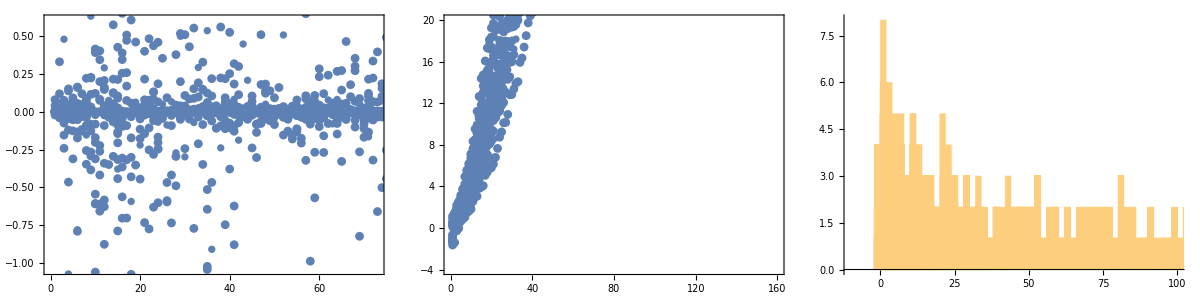

```mathematica
Grid[{{
Show[plts[[All,1]]],
Show[plts[[All,2]]],
Show[plts[[All,3]]]
}}]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

Normalise coupling blocks!!!!

```mathematica
CouplingBlockjs={};
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockj={};
CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockT={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb-1]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];

OutDim=Dimensions[tmp][[1]]/BareDims[[nb]][[1]];

test=ArrayReshape[tmp,{OutDim,BareDims[[nb]][[1]]}][[;;;;dH,;;;;dH]];
AppendTo[CouplingBlockT,{mIn,test}];
AppendTo[CouplingBlockTA,{mIn,test[[ActiveBasVFin[[nj]][[nb]],ActiveBasVHe3]]}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[anzBas]}];

AppendTo[CouplingBlockjs,CouplingBlockj];
AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim_active(⟨ψ|ο̂|helion⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim_bare(⟨ψ|ο̂|helion⟩)   = ",Table[Dimensions[CouplingBlockjs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[LitHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[LitNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

Dim_active(⟨ψ|ο̂|helion⟩) = {{{73,57},{72,57},{78,57},{75,57},{68,57},{84,57},{84,57},{72,57},{78,57}},{{92,57},{94,57},{85,57},{94,57},{83,57},{98,57},{96,57},{102,57},{102,57}}}

Dim_bare(⟨ψ|ο̂|helion⟩)   = {{{78,60},{72,60},{78,60},{76,60},{69,60},{84,60},{84,60},{72,60},{78,60}},{{95,60},{96,60},{86,60},{94,60},{84,60},{98,60},{96,60},{102,60},{102,60}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{73,73},{72,72},{78,78},{75,75},{68,68},{84,84},{84,84},{72,72},{78,78}},{{92,92},{94,94},{85,85},{94,94},{83,83},{98,98},{96,96},{102,102},{102,102}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{73,73},{72,72},{78,78},{75,75},{68,68},{84,84},{84,84},{72,72},{78,78}},{{92,92},{94,94},{85,85},{94,94},{83,83},{98,98},{96,96},{102,102},{102,102}}}

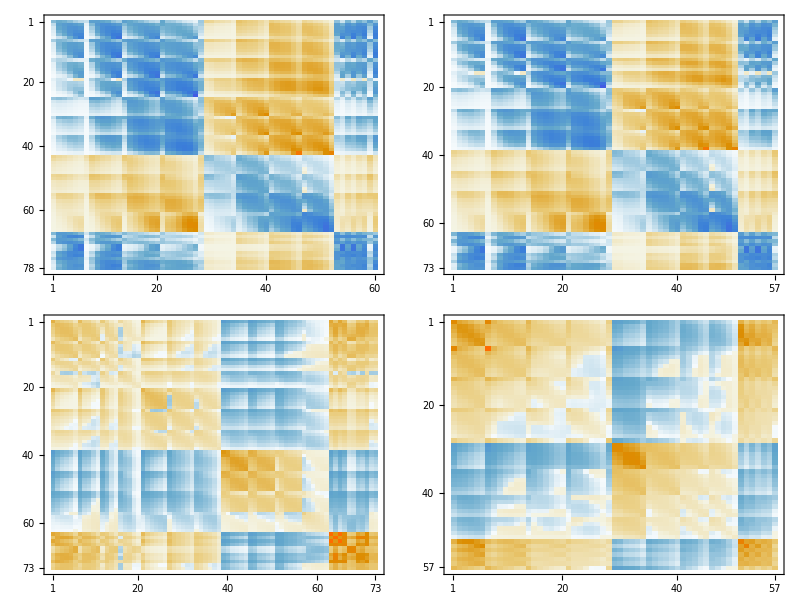

```mathematica
nb=1;nj=1;
Grid[{{
MatrixPlot[Chop[CouplingBlockjs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Coupling Matrix}",Magnification->2],ImageSize->Medium]
,
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Medium]
},{
MatrixPlot[Chop[LitHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Medium]
,
MatrixPlot[Chop[He3Ham],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Hamiltonian}",Magnification->2],ImageSize->Medium]
}}]
```

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
tmp=(Transpose[OμRHSEB].He3Ham).OμRHSEB; tmp=(tmp+Transpose[tmp])/2;
{λsHeEB,trfHeEB}=Eigensystem[tmp];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};evgsEB=OμRHSEB.evgsEB;
Print["ev=",TakeSmallest[λsHeEB,1][[1]]," norm=",evgsEB.He3Norm.evgsEB];
```

ev=-8.54733 norm=1.

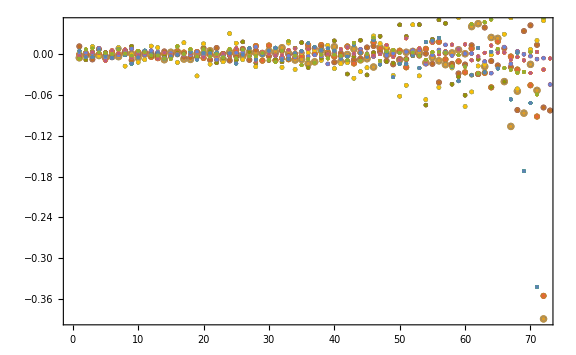

```mathematica
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
pltss={};
Do[
Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]][[nb]]];
tmp=(Transpose[OμLHSEB].LitHam[[nj]][[nb]]).OμLHSEB;
tmp=(tmp+Transpose[tmp])/2;
{λfinalEB,trfLitEB}=Eigensystem[tmp];
Do[
tmp=CouplingBlockjAs[[nj]][[nb]][[mm]][[2]];
AppendTo[inhomoEB[[nj]],Transpose[OμLHSEB].(tmp.evgsEB)];
,{mm,Range[1,Length[mIns[[nj]]]]}
];AppendTo[pltss,ListPlot[inhomoEB[[1]],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert O\\Big\\vert \\text{He}3 \\right\\rangle",Magnification->2]},ImageSize->Large]];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
Show[pltss]
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[tmp=(Transpose[OμRHSEV].He3Ham).OμRHSEV;(tmp+Transpose[tmp])/2];
EvecGSiEV=OμRHSEV.Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];
EvalGSiEV
{EvecGSiEV.He3Norm.EvecGSiEV,EvecGSiEV.He3Ham.EvecGSiEV}
```

-8.54733

{1.,-8.54733}

```mathematica
CumStrengthsJ={};pltsssJ={};
Do[
CumStrengths={};pltsss={};
Print[" J_final = ",Subscript[I, n][[nj]]];
Print["E_0^initial = ",EvalGSiEV,"    dim = ",Dimensions[EvalsIEV]];
Do[

{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]][[nb]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[tmp=(Transpose[OμLHSEV].(LitHam[[nj]][[nb]])).OμLHSEV;(tmp+Transpose[tmp])/2];
{EvalsFEV,EvecsFEV}=Sort[{EvalsFEV,EvecsFEV},#1[[1]]<#2[[1]]&];
EvecGSfEV=OμLHSEV.Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];


Print["Basisensemble ",nb,":  E_0^final  = ",EvalGSfEV,"    dim   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=Transpose[OμLHSEV].(CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].EvecGSiEV);

tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];
lpsisEV=Transpose[{EvalsFEV,tmplEV}];

CumStrengthsEV=Transpose[{Sort[lpsisEV][[All,1]],Accumulate[Sort[lpsisEV][[All,2]]]}];

pl1=
ListPlot[lpsisEV,Joined->False,PlotMarkers->{{♔,12},{♗,12}},PlotRange->{{-3,7.5},{0,Automatic}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize];
pl2=
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]];

AppendTo[pltsss,{pl1,pl2}];
AppendTo[CumStrengths,CumStrengthsEV];

,{nb,Range[anzBas]}
];
AppendTo[pltsssJ,pltsss];
AppendTo[CumStrengthsJ,CumStrengths];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

J_final = 0.5

E_0^initial = -8.54733    dim = {56}

Basisensemble 1:  E_0^final  = -1.64547    dim   = {72}

Basisensemble 2:  E_0^final  = 0.514781    dim   = {72}

Basisensemble 3:  E_0^final  = -0.768009    dim   = {77}

Basisensemble 4:  E_0^final  = 0.518251    dim   = {74}

Basisensemble 5:  E_0^final  = 0.109661    dim   = {67}

Basisensemble 6:  E_0^final  = 0.378606    dim   = {80}

Basisensemble 7:  E_0^final  = -1.06471    dim   = {84}

Basisensemble 8:  E_0^final  = 1.12614    dim   = {71}

Basisensemble 9:  E_0^final  = 0.892783    dim   = {75}

J_final = 1.5

E_0^initial = -8.54733    dim = {56}

Basisensemble 1:  E_0^final  = 0.338805    dim   = {90}

Basisensemble 2:  E_0^final  = -1.29049    dim   = {94}

Basisensemble 3:  E_0^final  = -1.12594    dim   = {85}

Basisensemble 4:  E_0^final  = -1.05376    dim   = {92}

Basisensemble 5:  E_0^final  = -0.984206    dim   = {83}

Basisensemble 6:  E_0^final  = -1.41619    dim   = {97}

Basisensemble 7:  E_0^final  = -0.650733    dim   = {92}

Basisensemble 8:  E_0^final  = -1.21584    dim   = {99}

Basisensemble 9:  E_0^final  = -1.20662    dim   = {102}

```mathematica
Integrate[8 Pi^2 x^2 (x Exp[-x^2/(4 α)-(ω-0.75 x^2)/α]/(3 Pi^1.5 α^2.5))^2/(2 √(ω-0.75 x^2)),{x,0,√(4. ω/3.)},Assumptions->{α∈Reals,α>0,ω∈Reals,ω>0}];

NielsF[ω_,α_]:=(ⅇ^(-(4 ω)/(3 α)) ((ω/α)^2 BesselI[0,(2 ω)/(3 α)]+((ω/α)^2-3 ω/α) BesselI[1,(2 ω)/(3 α)]))/(81 √3 α^2);
NielsC[λ_,α_]:=NIntegrate[NielsF[ω,α],{ω,0,λ}]

emin=-3;emax=164;
sc=0.975 (4 Pi/137)^-1;
αRGM=1.8;

lplts={};
Do[
AppendTo[lplts,ListPlot[#->Range[Length[EvalsFEV]]&/@CumStrengthsJ[[nj]],Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2],ImageSize->Large,PlotStyle->{Directive[Black,PointSize[0.005]],Directive[Blue,PointSize[0.005]]},PlotLegends->{"fds","sd"}]]
,{nj,Range[Length[Subscript[I, n]]]}];

Show[
ListPlot[#->Range[Length[EvalsFEV]]&/@CumStrengthsJ[[2]],Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["",Magnification->2],ImageSize->Large,PlotStyle->Directive[Blue,PointSize[0.005]],PlotLegends->"J=(3/2)^-"],
ListPlot[#->Range[Length[EvalsFEV]]&/@CumStrengthsJ[[1]],Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["",Magnification->2],ImageSize->Large,PlotStyle->Directive[Black,PointSize[0.005]],PlotLegends->"J=(1/2)^-"](*,
Plot[sc NielsC[λ/hbarsqO2m,αRGM]/fl,{λ,emin,emax},PlotRange->{{emin,emax},Automatic},PlotStyle->{Magenta,Thick},ImageSize->Large]*)
]
Put[CumStrengths,LocalObject["CumStr_05_15"]]
```

-Graphics-

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumStr_05_15]

```mathematica
ListPlot[lplts]
```

Part::partw: Part 2 of #1 does not exist.

-Graphics-

```mathematica
Cum1=Get[LocalObject["CumStr_mdHe-bound_FSon"]];
Cum2=Get[LocalObject["CumStr_mdHe-bound_FSon-2"]];

emin=-3;emax=5;

α1=1;
α2=2;
sc=0.975 (4 Pi/137)^-1;
hbarsqO2m=hbarc^2/(2 mn);
Show[
(*Plot[sc NielsC[λ/hbarsqO2m,α1],{λ,emin,emax},PlotRange->{{emin,emax},Full},PlotStyle->{Red,Thick}],
Plot[sc NielsC[λ/hbarsqO2m,α2],{λ,emin,emax},PlotRange->{{emin,emax},Full},PlotStyle->{Red,Thick}],*)
(*ListPlot[#->Range[Length[EvalsFEV]]&/@Cum1,Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Automatic},PlotStyle->Directive[Red,PointSize[Large]],AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2],PlotStyle->PointSize[0.005],PlotLegends->MaTeX["\\color{red}{\\text{1-d helion (unbound), FS}}",Magnification->2]],*)
ListPlot[#->Range[Length[EvalsFEV]]&/@Cum2,Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},PlotMarkers->"OpenMarkers",PlotStyle->Directive[Black,PointSize[Large]],
AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left(\\omega\\right)d\\omega",Magnification->2]},PlotStyle->PointSize[0.005],PlotLegends->MaTeX["B\\left(~^3\\text{He}~,~S,P,D-\\text{wave}~,~V_4~,~\\text{dim}\\approx 217~\\right)\\approx8.01~\\text{MeV}, ",Magnification->2]]
,
ListPlot[#->Range[Length[EvalsFEV]]&/@Cum1
,Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Automatic},PlotStyle->Directive[Blue,PointSize[Large]],PlotLegends->MaTeX["B\\left(~^3\\text{He}~,~S-\\text{wave}~,~V_4~,~\\text{dim}\\approx 30~\\right)\\approx8.37~\\text{MeV} ",Magnification->2]]
]
```

-Graphics-